# Thesis Project: Cement Hydrates C-H-S

## K-Points Analysis

### Working directory

```mathematica
wrkdir = "/home/qbit/Documents/git-repositories/bachelor-thesis/";
SetDirectory[wrkdir]
```

/home/qbit/Documents/git-repositories/bachelor-thesis

### The k-point grid

```mathematica
bulk = Import["./dftb/eos/POSCAR-init", "Table"];
```

```mathematica
lattbulk = bulk[[2, 1]] bulk[[3;;5]]
```

{{13.5354,0.18446,0.00755401},{-16.2629,24.8887,-0.00875423},{0.543338,-0.483321,23.4374}}

```mathematica
{a, b, c} = lattbulk;
```

```mathematica
Δk = Table[0.07-0.005 i, {i, 0, 10}];
```

```mathematica
Δk//Map[{#, Round[((b×c)/((a×b).c)//Norm)/#],
Round[((c×a)/((a×b).c)//Norm)/#],
Round[((a×b)/((a×b).c)//Norm)/#]}&, #]&//TableForm
```

0.07 | 1 | 1 | 1
0.065 | 1 | 1 | 1
0.06 | 1 | 1 | 1
0.055 | 2 | 1 | 1
0.05 | 2 | 1 | 1
0.045 | 2 | 1 | 1
0.04 | 2 | 1 | 1
0.035 | 2 | 1 | 1
0.03 | 3 | 1 | 1
0.025 | 3 | 2 | 2
0.02 | 4 | 2 | 2

We will run the xkp.sh script for k-points densities 0.06, 0.04, and 0.03

### Convergency of k-points

```mathematica
data = Import["./dftb/kp.dat"]
```

{{1,-4660.48,43},{2,-4660.51,58},{3,-4660.51,37}}

```mathematica
kpdat =data[[All,{1,2}]]//Map[#/{1,690}&]
```

{{1,-6.75432},{2,-6.75437},{3,-6.75436}}

#### Get the x and y data:

```mathematica
kpY=kpdat[[All,2]]
kpX={0.06,0.04,0.03}
```

{-6.75432,-6.75437,-6.75436}

{0.06,0.04,0.03}

#### Plot the data:

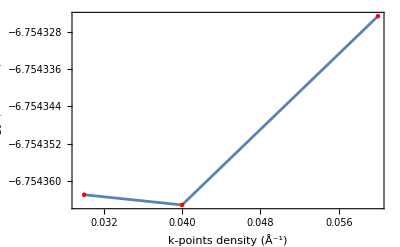

```mathematica
ListPlot[
Transpose[{kpX,kpY}],
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Red]},
Frame->True,
FrameLabel->
{"k-points density (Å^-1)", "Energy (eV/atom)"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400]
```

#### Let’s analyse the convergency of these data using the 1 meV/atom criteria

```mathematica
energyMin=kpdat[[1,2]]+10^-3/2;
energyMax=kpdat[[1,2]]-10^-3/2;
```

```mathematica
kPlot=ListPlot[
Transpose[{kpX,kpY}],
PlotRange->{kpdat[[1,2]]+10^-3, kpdat[[1,2]]-10^-3},
Joined->True,
Mesh->Full,
MeshStyle->
{Directive[PointSize[Medium], Red]},
Frame->True,
FrameLabel->
{"k-points density (Å^-1)", "Energy (eV/atom)"},
BaseStyle->
{FontFamily->"HelveticaNeue", FontSize->15},
ImageSize->400];
```

```mathematica
energyWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{0.02,energyMin},{0.07,energyMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{0.02,energyMin},{0.07,energyMin}}]},{Dashed,Black,Line[{{0.02,energyMax},{0.07,energyMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{0.05,energyMin},{0.05,energyMax}}]},Text[Style["1 meV",FontSize->12,Black],{0.053,0.0001+Mean[{energyMin,energyMax}]}]}];
```

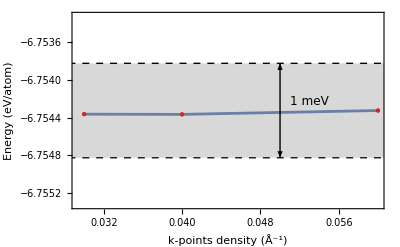

```mathematica
Show[kPlot, energyWindow]
```

From this result, we use from now on the k-point grid 1x1x1

## Cut-off Energy Analysis

### ENCUT

```mathematica
datacem = Import["./dftb/ecut.dat"]
```

{{300,-3825.1,29},{350,-4418.95,15},{400,-4604.35,14},{450,-4649.03,13},{500,-4657.13,10},{550,-4658.2,8},{600,-4658.69,7},{650,-4659.16,7},{700,-4659.66,7},{750,-4660.05,7},{800,-4660.48,6},{850,-4660.84,6},{900,-4661.14,6}}

```mathematica
dataecut=datacem[[All,{1,2}]]//Map[#/{1,690}&]
```

{{300,-5.54362},{350,-6.40428},{400,-6.67298},{450,-6.73773},{500,-6.74946},{550,-6.75101},{600,-6.75173},{650,-6.7524},{700,-6.75314},{750,-6.75369},{800,-6.75432},{850,-6.75484},{900,-6.75527}}

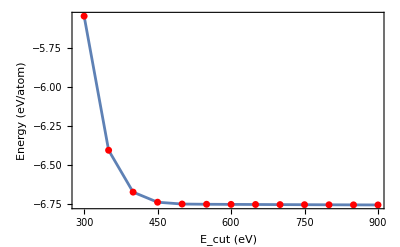

```mathematica
dataecut//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->[{}],
InterpolationOrder->1,
ImageSize->400,
Epilog->
{Red, AbsolutePointSize[5],
Point[#]}
]&
```

We  use meV precision because magnetic properties are really tiny. So we need this precision to describe these properties.

```mathematica
encutMin=dataecut[[13,2]];
encutMax=dataecut[[13,2]]+10^-3;
```

```mathematica
encutPlot =dataecut//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (meV/atom)" },
BaseStyle->{FontFamily -> "Helvetica", 
FontSize->15},
Joined->True,
PlotRange->{{700,950},{dataecut[[13,2]], dataecut[[10,2]]}},
InterpolationOrder->1,
ImageSize->400,
Epilog->
{Red, AbsolutePointSize[5],
Point[#]}
]&;
```

```mathematica
encutWindow=Graphics[{(*Shaded rectangle*){Gray,Opacity[0.3],Rectangle[{200,encutMin},{950,encutMax}]},(*Dashed lines for rectangle edges*){Dashed,Black,Line[{{200,encutMin},{950,encutMin}}]},{Dashed,Black,Line[{{200,encutMax},{950,encutMax}}]},(*Double-headed arrow with annotation*){Arrowheads[{-0.02,0.02}],Arrow[{{750,encutMin},{750,encutMax}}]},Text[Style["1 meV",FontSize->12,Black],{800,Mean[{encutMin,encutMax}]}]}];
```

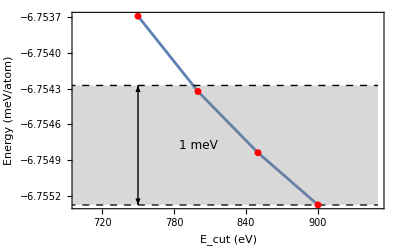

```mathematica
Show[encutPlot,encutWindow]
```

We  use 800 meV for  CSH analysis from now on.

## Density of States

```mathematica
pdosData=Import["./cluster-files/DOSCAR-cem1.sto", "Table"];
```

```mathematica
Dimensions[pdosData]
```

{2074387}

```mathematica
dos = pdosData[[7;;7+3000]][[All, {1, 2}]];
```

```mathematica
ef = pdosData[[6, 4]]
```

3.069

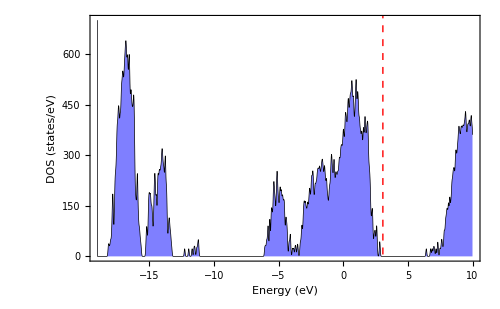

```mathematica
ListPlot[dos, 
Joined->True,
Axes->False,
Frame->True,
FrameLabel->
{"Energy (eV)", 
"DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle-> 
Directive[Red, Dashed,
AbsoluteThickness[1]],
BaseStyle->
{FontFamily->"Helvetica",
FontSize->15},
Filling->Axis,
FillingStyle->
Directive[Opacity[0.5], Blue],
PlotStyle-> 
{AbsoluteThickness[0.5], Black},
ImageSize->500,
PlotRange->{All, {0, 700}}
]
```

### Partial Density of States PDOS

Let us define the number of atoms of each element.

```mathematica
atomsCa=99;
atomsSi=60;
atomsO=323;
atomsH=208;
```

## Benchmark

```mathematica
benchRes=Import["./cluster-files/results.dat"]
```

{{1,552.512},{2,308.492},{3,235.218},{5,186.864},{7,213.865},{9,187.9},{11,268.706}}

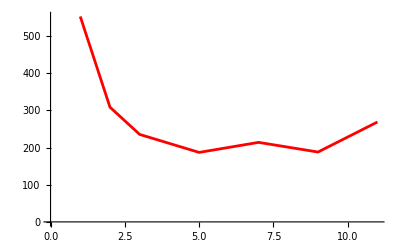

```mathematica
ListPlot[bechRes,Joined->True,PlotStyle->{Red,PointSize[0.5]}]
```

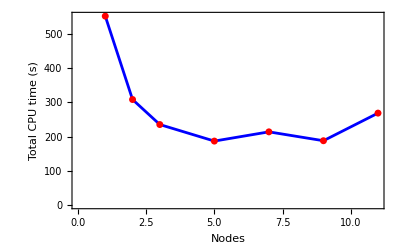

```mathematica
ListPlot[benchRes,
Frame->True,
FrameLabel->{"Nodes","Total CPU time (s)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Joined->True,InterpolationOrder->1,ImageSize->400,
PlotStyle->Blue,
Epilog->{Red,AbsolutePointSize[5],Point[benchRes]}]
```